```mathematica
(*4.1*)
(*Гиринский1*)
Qg1[k_,b_,μ_,pk_,pc_, rc_]=(2 π k b)/μ *(pk-pc)/Log[(1.66 b)/rc];
(*Маскет*)
ϕ[x_]=Log[(Gamma[0.875 x] Gamma[0.125 x])/(Gamma[1-0.875 x] Gamma[1-0.125 x])];
h[b_,hh_]=b/hh;
ξ[b_,rc_,hh_,Rk_]=1/(2 h[b,hh])*(2 Log[(4 hh)/rc]-ϕ[h[b,hh]])-Log[(4 hh)/Rk];
Qg2[k_,μ_,hh_,b_,rc_,Rk_,pk_,pc_]=(2 π k hh)/μ *(pk-pc)/ξ[b,rc,hh,Rk];
(*Козени*)
QK[k_,μ_,hh_,b_,Rk_,rc_,pk_,pc_]=(2 π k hh h[b,hh])/μ*(pk-pc)/Log[Rk/rc]*(1+7 √(rc/(2 hh h[b,hh])) Cos[(π h[b,hh])/2]);
(*Чарного*)
QCH[k_,μ_,hh_,b_,Rk_,rc_,pk_,pc_,R0_]=(2 π k hh)/μ*(pk-pc)/(Log[Rk/R0]+hh/rc-hh/R0);
```

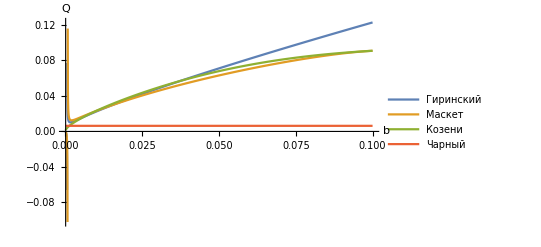

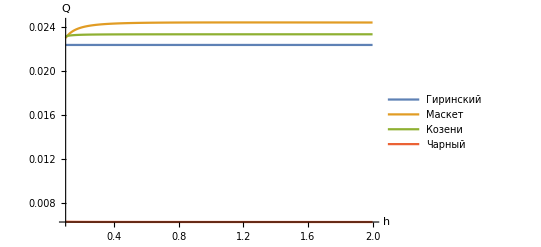

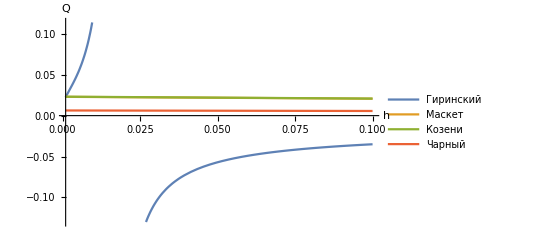

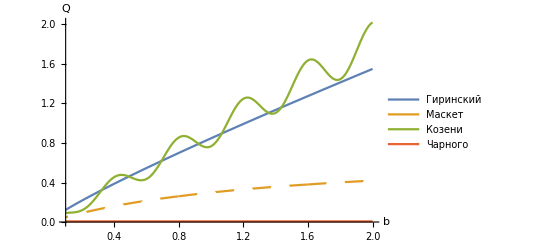

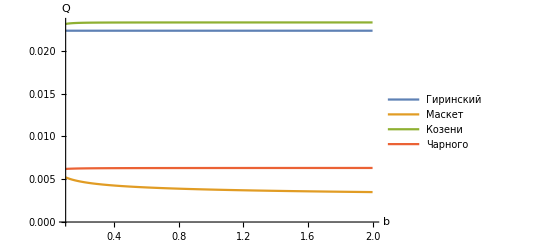

```mathematica
pk1=1;
pc1=0;
Rk1=1;
rc1=0.001Rk1;
hh1=0.1 Rk1;
b1=0.01;
k1=1;
μ1=1;
R01=1.5 Rk1;
Plot[{Qg1[k1,y,μ1,pk1,pc1, rc1],Qg2[k1,μ1,hh1,y,rc1,Rk1,pk1,pc1],QK[k1,μ1,hh1,y,Rk1,rc1,pk1,pc1],QCH[k1,μ1,hh1,y,Rk1,rc1,pk1,pc1,R01]},{y,0.0001,hh1},AxesLabel-> {b,Q}, PlotLegends->{"Гиринский","Маскет","Козени","Чарный"}]
Plot[{Qg1[k1,b1,μ1,pk1,pc1, rc1],Qg2[k1,μ1,y,b1,rc1,Rk1,pk1,pc1],QK[k1,μ1,y,b1,Rk1,rc1,pk1,pc1],QCH[k1,μ1,y,b1,Rk1,rc1,pk1,pc1,R01]},{y,0.1,2},AxesLabel-> {h,Q}, PlotLegends->{"Гиринский","Маскет","Козени","Чарный"}]
Plot[{Qg1[k1,b1,μ1,pk1,pc1, y],Qg2[k1,μ1,hh1,b1,rc1,Rk1,pk1,y],QK[k1,μ1,hh1,b1,Rk1,rc1,pk1,y],QCH[k1,μ1,hh1,b1,Rk1,rc1,pk1,y,R01]},{y,0.001,0.1},AxesLabel-> {h,Q}, PlotLegends->{"Гиринский","Маскет","Козени","Чарный"}]
```

```mathematica
(*4.2*)
(*Борисов*)
QB[k_,b_,μ_,Δp_, rc_,Rk_,l_]=(2 π k hh)/μ*Δp/(Log[2 Rk/l]+h/(2 l)Log[hh/(2 π rc)]);
(*Joshi*)
a[l_,Rk_]=l*√(0.5+√(0.25+(Rk/l)^4));
QD[k_,μ_,hh_,Δp_,l_,Rk_,rc_]=(2 π k hh)/μ*Δp/(Log[(a[l,Rk]+√((a^2)[l,Rk]-l^2))/l]+hh/(2l)Log[hh/(2 rc)]);
```

```mathematica
pk1=1;
pc1=0;
Rk1=1;
rc1=0.001Rk1;
hh1=0.1 Rk1;
b1=0.01;
k1=1;
μ1=1;
R01=1.5 Rk1;
(*l1=0.5 Rk1;*)
Δp=1;
Plot[{QB[k1,b1,μ1,Δp,rc1,Rk1,l1],QD[k1,μ1,hh1,Δp,l1,Rk1,rc1]},{l1,0.0001,hh1},AxesLabel-> {b,Q}, PlotLegends->{"Гиринский","Маскет","Козени","Чарный"}]
```

-Graphics-